```mathematica
PAYOUTSTRUCTURE = {{10,10,10},{0,0,20},{0,20,0},{0,3,3},{20,0,0},{3,0,3},{3,3,0},{1,1,1}};
(*                   CCC           CCD      CDC       CDD       DCC       DCD       DDC      DDD       *)
LABELS={"CCC","CCD","CDC","CDD","DCC","DCD","DDC","DDD"};
CalculateFitness[one_,two_,three_,player_]:=
Module[{playerOneStrat,playerTwoStrat,playerThreeStrat,transitionTable,longTerm},
playerOneStrat=one;
playerTwoStrat=two;
playerThreeStrat=three;
transitionTable=CreateTransitionTable[playerOneStrat,playerTwoStrat,playerThreeStrat];
vec=Re[Eigenvectors[Transpose[transitionTable],1][[1]]];
vec=vec/Total[vec];
vec.PAYOUTSTRUCTURE[[All,player]]
];

CreateTransitionTable[stratOne_,stratTwo_,stratThree_]:=
Table[
Flatten[Outer[Times,stratOne[[i]],stratTwo[[i]],stratThree[[i]]]]
,{i,1,Length[stratOne]}];


MutationDistribution=TruncatedDistribution[{0,1},NormalDistribution[μ,σ]];
Mutation[prisonStrategy_,mutationDeviation_]:=
Module[{chanceOfMutation,newDefect,inputStrategy,temp,newPrisonStrat,newCoop,mutatedStrat},
inputStrategy=prisonStrategy;
Table[
chanceOfMutation=RandomReal[{0,1}];
newCoop=Which[
chanceOfMutation≤1/16,RandomVariate[MutationDistribution/.{μ->inputStrategy[[i,1]],σ->mutationDeviation}],
chanceOfMutation≤1/8,RandomReal[{0,1}],
True,inputStrategy[[i,1]]
];
{newCoop,1-newCoop}
,{i,1,8}]
];

evaluateGeneration[population_,opposingStratOne_,opposingStratTwo_,mutability_,player_]:=
Module[{profileOne,profileTwo,mutatedPopulation},
mutatedPopulation=Mutation[#,mutability]&/@population;
Table[
profileOne =RandomChoice[mutatedPopulation];
profileTwo =RandomChoice[mutatedPopulation];
Which[
player==1,
Which[
CalculateFitness[profileOne,opposingStratOne,opposingStratTwo,player]≥CalculateFitness[profileTwo,opposingStratOne,opposingStratTwo,player],
profileOne,
CalculateFitness[profileTwo,opposingStratOne,opposingStratTwo,player]≥CalculateFitness[profileOne,opposingStratOne,opposingStratTwo,player],
profileTwo
],
player==2,
Which[
CalculateFitness[opposingStratOne,profileOne,opposingStratTwo,player]≥CalculateFitness[opposingStratOne,profileTwo,opposingStratTwo,player],
profileOne,
CalculateFitness[opposingStratOne,profileTwo,opposingStratTwo,player]≥CalculateFitness[opposingStratOne,profileOne,opposingStratTwo,player],
profileTwo
],
player==3,
Which[
CalculateFitness[opposingStratOne,opposingStratTwo,profileOne,player]≥CalculateFitness[opposingStratOne,opposingStratTwo,profileTwo,player],
profileOne,
CalculateFitness[opposingStratOne,opposingStratTwo,profileTwo,player]≥CalculateFitness[opposingStratOne,opposingStratTwo,profileOne,player],
profileTwo
]
]
,{i,1,Length[population]}]
];

GenerateStrategeyTable[numStrats_]:=
Table[
Table[
z = RandomReal[];
{z,1-z}
,{8}]
,numStrats];
```

### Test Code

```mathematica
Null
```

#### Actual / Final Code

```mathematica
populationSize=250;
populationOne=GenerateStrategeyTable[populationSize];
populationTwo=GenerateStrategeyTable[populationSize];
populationThree=GenerateStrategeyTable[populationSize];
mutability=0.05;
snapShotPop=ConstantArray[0,populationSize];
generations=200;
checkSetOne=ConstantArray[0,generations/50];
checkSetTwo=ConstantArray[0,generations/50];
checkSetThree=ConstantArray[0,generations/50];
counter=1;
Do[
snapShotOne=RandomChoice[populationOne];
snapShotTwo=RandomChoice[populationTwo];
snapShotThree=RandomChoice[populationThree];
populationOne=evaluateGeneration[populationOne,snapShotTwo,snapShotThree,mutability,1];
populationTwo=evaluateGeneration[populationTwo,snapShotOne,snapShotThree,mutability,2];
populationThree=evaluateGeneration[populationThree,snapShotOne,snapShotTwo,mutability,3];
If[Mod[i,50]==0,
checkSetOne[[counter]]=First[Commonest[populationOne]];
checkSetTwo[[counter]]=First[Commonest[populationOne]];
checkSetThree[[counter]]=First[Commonest[populationOne]];
counter++;
]
,{i,1,generations}
];
```

```mathematica
checkSetOne//MatrixForm
checkSetTwo//MatrixForm
checkSetThree//MatrixForm
```

((0.904748
0.0952521) | (0.259936
0.740064) | (0.0991897
0.90081) | (0.311334
0.688666) | (0.0305553
0.969445) | (0.178271
0.821729) | (0.140937
0.859063) | (0.0185052
0.981495)
(0.663696
0.336304) | (0.152073
0.847927) | (0.265761
0.734239) | (0.138031
0.861969) | (0.066411
0.933589) | (0.00567748
0.994323) | (0.865516
0.134484) | (0.236659
0.763341)
(0.887039
0.112961) | (0.274178
0.725822) | (0.293758
0.706242) | (0.00243615
0.997564) | (0.930063
0.0699368) | (0.11418
0.88582) | (0.315933
0.684067) | (0.0216336
0.978366)
(0.658734
0.341266) | (0.847336
0.152664) | (0.0815981
0.918402) | (0.0215018
0.978498) | (0.0580394
0.941961) | (0.0787438
0.921256) | (0.0389052
0.961095) | (0.0399784
0.960022))

((0.904748
0.0952521) | (0.259936
0.740064) | (0.0991897
0.90081) | (0.311334
0.688666) | (0.0305553
0.969445) | (0.178271
0.821729) | (0.140937
0.859063) | (0.0185052
0.981495)
(0.663696
0.336304) | (0.152073
0.847927) | (0.265761
0.734239) | (0.138031
0.861969) | (0.066411
0.933589) | (0.00567748
0.994323) | (0.865516
0.134484) | (0.236659
0.763341)
(0.887039
0.112961) | (0.274178
0.725822) | (0.293758
0.706242) | (0.00243615
0.997564) | (0.930063
0.0699368) | (0.11418
0.88582) | (0.315933
0.684067) | (0.0216336
0.978366)
(0.658734
0.341266) | (0.847336
0.152664) | (0.0815981
0.918402) | (0.0215018
0.978498) | (0.0580394
0.941961) | (0.0787438
0.921256) | (0.0389052
0.961095) | (0.0399784
0.960022))

((0.904748
0.0952521) | (0.259936
0.740064) | (0.0991897
0.90081) | (0.311334
0.688666) | (0.0305553
0.969445) | (0.178271
0.821729) | (0.140937
0.859063) | (0.0185052
0.981495)
(0.663696
0.336304) | (0.152073
0.847927) | (0.265761
0.734239) | (0.138031
0.861969) | (0.066411
0.933589) | (0.00567748
0.994323) | (0.865516
0.134484) | (0.236659
0.763341)
(0.887039
0.112961) | (0.274178
0.725822) | (0.293758
0.706242) | (0.00243615
0.997564) | (0.930063
0.0699368) | (0.11418
0.88582) | (0.315933
0.684067) | (0.0216336
0.978366)
(0.658734
0.341266) | (0.847336
0.152664) | (0.0815981
0.918402) | (0.0215018
0.978498) | (0.0580394
0.941961) | (0.0787438
0.921256) | (0.0389052
0.961095) | (0.0399784
0.960022))

```mathematica
a=Table[
CreateTransitionTable[checkSetOne[[i]],checkSetTwo[[i]],checkSetThree[[i]]]
,{i,1,generations/50}];
a[[4]]//MatrixForm
```

(0.285845 | 0.148086 | 0.148086 | 0.0767178 | 0.148086 | 0.0767178 | 0.0767178 | 0.0397447
0.608368 | 0.10961 | 0.10961 | 0.0197484 | 0.10961 | 0.0197484 | 0.0197484 | 0.00355806
0.000543301 | 0.00611495 | 0.00611495 | 0.0688249 | 0.00611495 | 0.0688249 | 0.0688249 | 0.774637
9.94091×10^-6 | 0.000452388 | 0.000452388 | 0.0205871 | 0.000452388 | 0.0205871 | 0.0205871 | 0.936872
0.00019551 | 0.00317306 | 0.00317306 | 0.0514978 | 0.00317306 | 0.0514978 | 0.0514978 | 0.835792
0.000488258 | 0.00571233 | 0.00571233 | 0.0668309 | 0.00571233 | 0.0668309 | 0.0668309 | 0.781882
0.0000588873 | 0.00145472 | 0.00145472 | 0.0359368 | 0.00145472 | 0.0359368 | 0.0359368 | 0.887766
0.0000638965 | 0.00153438 | 0.00153438 | 0.0368458 | 0.00153438 | 0.0368458 | 0.0368458 | 0.884796)

```mathematica
b=Table[
vec=Re[Eigenvectors[Transpose[a[[i]]],1][[1]]];
vec/Total[vec]
,{i,1,generations/50}];
b//MatrixForm
```

(0.00435409 | 0.00386649 | 0.00386649 | 0.0272227 | 0.00386649 | 0.0272227 | 0.0272227 | 0.902378
0.100338 | 0.0496287 | 0.0496287 | 0.0980501 | 0.0496287 | 0.0980501 | 0.0980501 | 0.456625
0.0165134 | 0.00483028 | 0.00483028 | 0.0263662 | 0.00483028 | 0.0263662 | 0.0263662 | 0.889897
0.00197266 | 0.00218638 | 0.00218638 | 0.0374693 | 0.00218638 | 0.0374693 | 0.0374693 | 0.87906)

```mathematica
f=Table[
fitOne=CalculateFitness[checkSetOne[[i]],checkSetTwo[[i]],checkSetThree[[i]],1];
fitTwo=CalculateFitness[checkSetTwo[[i]],checkSetOne[[i]],checkSetThree[[i]],2];
fitThree=CalculateFitness[checkSetThree[[i]],checkSetOne[[i]],checkSetTwo[[i]],3];
{fitOne,fitTwo,fitThree},
{i,1,generations/50}];
f//MatrixForm;
b[[4]]
f[[4]]
```

{0.00197266,0.00218638,0.00218638,0.0374693,0.00218638,0.0374693,0.0374693,0.87906}

{1.16733,1.16733,1.16733}

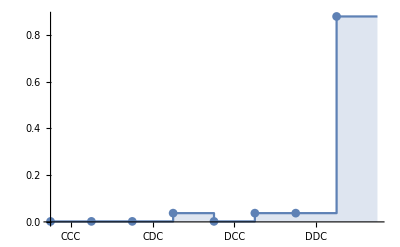

```mathematica
ListStepPlot[b[[4]],Filling->Axis,AxesOrigin->{1,0},PlotMarkers->Automatic,PlotRange->All,Ticks->{{{1.5,"CCC"},{2.5,"CCD"},{3.5,"CDC"},{4.5,"CDD"},{5.5,"DCC"},{6.5,"DCD"},{7.5,"DDC"},{8.5,"DDD"}},Automatic}]
```

```mathematica
checkSetOne[[1]];
checkSetTwo[[1]];
a//MatrixForm;
b//MatrixForm;
c//MatrixForm;
c=GenerateStrategeyTable[1];
a=GenerateStrategeyTable[1];
b=GenerateStrategeyTable[1];
z=CreateTransitionTable[a[[1]],b[[1]],c[[1]]];
z//MatrixForm
Table[
Accumulate[z[[i]]]
,{i,1,8}]//MatrixForm;
CalculateFitness[a[[1]],b[[1]],c[[1]],1]
```

(0.276212 | 0.0692487 | 0.068983 | 0.0172946 | 0.363555 | 0.0911463 | 0.0907966 | 0.0227635
0.156031 | 0.155176 | 0.0502116 | 0.0499362 | 0.22328 | 0.222055 | 0.0718524 | 0.0714583
0.416991 | 0.129443 | 0.338913 | 0.105205 | 0.00397718 | 0.0012346 | 0.00323248 | 0.00100343
0.138125 | 0.18536 | 0.206799 | 0.277519 | 0.0328634 | 0.0441019 | 0.0492026 | 0.0660288
0.0504731 | 0.0233183 | 0.547022 | 0.252722 | 0.00730717 | 0.00337588 | 0.0791943 | 0.0365874
0.0410356 | 0.036689 | 0.0337042 | 0.0301341 | 0.24884 | 0.222482 | 0.204382 | 0.182733
0.0554038 | 0.510699 | 0.00830242 | 0.0765298 | 0.0297104 | 0.273863 | 0.00445219 | 0.0410392
0.191137 | 0.0220767 | 0.0568374 | 0.00656485 | 0.499846 | 0.0577333 | 0.148637 | 0.0171679)

3.07903

```mathematica
z=CreateTransitionTable[b[[1]],a[[1]],c[[1]]];
z//MatrixForm
```

(0.0995649 | 0.16956 | 0.00805317 | 0.0137146 | 0.242709 | 0.413335 | 0.0196312 | 0.0334321
0.00296406 | 0.00571122 | 0.00410736 | 0.00791416 | 0.140249 | 0.270236 | 0.194347 | 0.374471
0.540278 | 0.214736 | 0.0248498 | 0.00987665 | 0.143844 | 0.0571712 | 0.006616 | 0.00262956
0.130814 | 0.18535 | 0.0709177 | 0.100483 | 0.137486 | 0.194805 | 0.0745351 | 0.105609
0.0534227 | 0.189538 | 0.00949537 | 0.0336886 | 0.133275 | 0.472847 | 0.0236884 | 0.0840441
0.000580801 | 0.0381006 | 0.0128494 | 0.842921 | 0.000068536 | 0.00449597 | 0.00151626 | 0.0994669
0.0403773 | 0.613673 | 0.016383 | 0.248996 | 0.00353831 | 0.0537769 | 0.00143566 | 0.0218198
0.583457 | 0.275843 | 0.0845436 | 0.03997 | 0.00959922 | 0.00453826 | 0.00139094 | 0.000657599)

```mathematica
z=CreateTransitionTable[c[[1]],b[[1]],a[[1]]];
z//MatrixForm
```

(0.000077894 | 0.0190567 | 0.003787 | 0.926486 | 4.15088×10^-6 | 0.00101551 | 0.000201805 | 0.0493713
0.0435433 | 0.39545 | 0.0109133 | 0.0991118 | 0.0357678 | 0.324835 | 0.0089645 | 0.0814136
0.0686165 | 0.309501 | 0.00887586 | 0.0400355 | 0.0920668 | 0.415277 | 0.0119093 | 0.053718
0.0498883 | 0.0834379 | 0.289476 | 0.484148 | 0.00511835 | 0.00856041 | 0.0296992 | 0.0496717
0.163387 | 0.0237004 | 0.432331 | 0.0627125 | 0.0761375 | 0.0110443 | 0.201464 | 0.0292237
0.236125 | 0.431294 | 0.0898969 | 0.164202 | 0.0201099 | 0.0367319 | 0.00765621 | 0.0139845
0.01528 | 0.0384569 | 0.00888556 | 0.0223633 | 0.164515 | 0.414053 | 0.0956679 | 0.240778
0.0945791 | 0.211074 | 0.189276 | 0.422411 | 0.00852241 | 0.0190196 | 0.0170554 | 0.0380629)